```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->14,FontFamily->"Times"},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.004]],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
logticksx=Join[{Log10@#,Switch[#,10^-1,0.1,1,1,10,10,_,Superscript[10,Log10@#]],{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
logticksx2=Join[{Log10@#,"",{.016,0}}&/@(10^Range[-30,33,1]),{Log10@#,"",{.008,0}}&/@Flatten[(10^Range[-30,33,1])*#&/@Range[2,9,1]]];
Msunt = ToString[Subscript["M","⊙"],FormatType->StandardForm];
```

```mathematica
hmf = ReadList[NotebookDirectory[]<>"hmf.dat",Table[Number,{3}]];
hmfi = Interpolation[hmf]
```

17
InterpolatingFunction[{{0.01, 20.}, {100000., 1. 10  }}, <>]

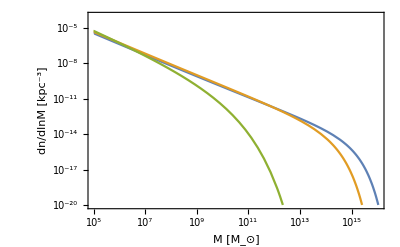

```mathematica
LogLogPlot[{hmfi[0.01,m],hmfi[1.,m],hmfi[10.,m]},{m,hmfi[[1,2,1]],hmfi[[1,2,2]]},FrameLabel->{"M ["<>Msunt<>"]","dn/dlnM [kpc^-3]"},PlotRange->{All,{1.*^-20,1.*^-4}}]
```

```mathematica
N1 = ReadList[NotebookDirectory[]<>"N1.dat",Table[Number,{3}]];
N1[[-1,3]]
LLN1i = Interpolation[Log10@N1[[All,{1,2}]]]
LLN1cumi = Interpolation[{Log10@#[[1]],#[[3]]/N1[[-1,3]]}&/@N1[[1;;-2]]]
```

32.2191

InterpolatingFunction[…]

InterpolatingFunction[…]

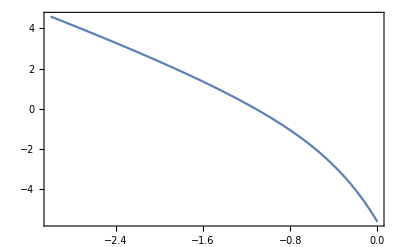

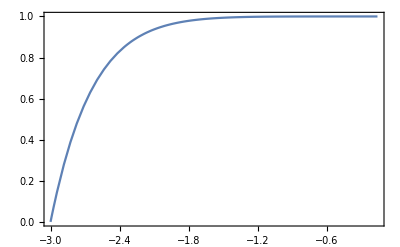

```mathematica
Plot[LLN1i[x],{x,LLN1i[[1,1,1]],LLN1i[[1,1,2]]}]
Plot[LLN1cumi[x],{x,LLN1cumi[[1,1,1]],LLN1cumi[[1,1,2]]},PlotRange->All]
```

```mathematica
P = ReadList[NotebookDirectory[]<>"lnmu.dat",Number];
```

```mathematica
Max@P
```

0.950067

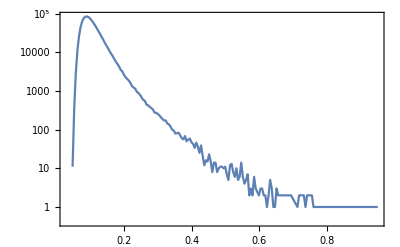

```mathematica
ListLogPlot[Sort@Tally[Round[P,Max@P/200]],Joined->True,PlotRange->All]
```